## Board

```mathematica
board=Array[
randLess[8]&,
{2,5,5}];
```

```mathematica
randLess[n_]:=With[{x=RandomInteger[{0,9}]},
If[x==n,randLess[n],x]
]
```

## Deck

```mathematica
(* functions are lists that indicate row column effected and pure function used *)
```

```mathematica
functions={ (* RandomSample@ *)
{{All,All},board ↦Map[x↦x+1,board]},
{{All,All},board ↦Map[x↦x-1,board]},
{{All,All},board↦Thread[Minus[board[[4]]]]},
{{1,All},board ↦Fold[Plus[#1,#2]&,board[[1]]]},
{{1,All},board ↦Fold[Subtract[#1,#2]&,board[[1]]]},
{{All,All},board ↦Array[Fibonacci[#]&,{Length@First[board]}]},
{{All,All},board ↦Array[-Fibonacci[#]&,{Length@First[board]}]},
{{All,All},board ↦Nest[Times[#,-1]&,board,5]},
{{1,All},board ↦Nest[Times[#,2]&,board[[1]],2]},
{{All,3},board ↦Map[BitXor[#,15]&,board[[All,3]]]},
{{2,All},board ↦BitShiftLeft/@board[[2]]},
{{2,All},board ↦BitShiftRight/@board[[2]]},
{{3,All},board ↦Map[First[board[[All,2]]+#]&,board[[3]]]},
{{1,All},board ↦First[board]+Total[Select[First[board],EvenQ[#]&]]},
{{All,3},board ↦Array[Length@board[[All,3]]&,Length@board[[All,3]]]},
{{All,All},board ↦Transpose[board]},
{{All,All},board ↦Nest[Transpose,board,555]},
{{All,All},board ↦RandomInteger[{Max[board],9},{3,3}]},
{{All,5},board ↦Differences[board[[All,5]]]},
{{All,2},board ↦Differences[board[[All,2]]]},
{{All,All},board ↦Count[Flatten@board,n_/;EvenQ[n]]},
{{4,All},board↦Permutations[Range[board[[4]]]]//Length}
};
```

```mathematica
deck=Part[{functions[[1;;5]],functions=functions[[6;;]]},1];
```

## State

```mathematica
t = 1;
score={0,0};
```

## Update

```mathematica
turn:=Set[t,Mod[t,2]+1]
```

```mathematica
updateScore:=Set[
score,
{Select[Flatten[board[[1]]],#==8&]//Length,
Select[Flatten[board[[2]]],#==8&]//Length}
];
```

```mathematica
rollDeck:=If[Length[functions]>0,
AppendTo[deck,
Part[{First[functions],functions=Rest[functions]},1]
]]
```

```mathematica
move[number_]:={
With[{choice=deck[[number]]},
board[[t]][[Part[choice,1,1],Part[choice,1,2]]]=choice[[2]][board[[t]]]
],
turn,updateScore, rollDeck,
deck=Delete[deck,number],board=mod[board]
}
```

```mathematica
(* same as move function but with flipped t value *)
attack[number_]:={
With[{choice=deck[[number]],tt=Mod[t,2]+1},
board[[tt]][[Part[choice,1,1],Part[choice,1,2]]]=choice[[2]][board[[tt]]]
],
turn,updateScore, rollDeck,
deck=Delete[deck,number],board=mod[board]
}
```

## Helper Functions

```mathematica
(* calculate and display player turn or game over msg *)
```

```mathematica
p={Style["It's player one's turn",FontSize->Large],
Style["It's player two's turn",FontSize->Large]};
```

```mathematica
winnerMsg={
Style["Game Over. It was a tie",FontSize->Large],
Style["Game Over. Player one wins!",FontSize->Large],
Style["Game Over. Player two wins!",FontSize->Large]
};
```

```mathematica
getWinner:=If[score[[1]]==score[[2]],
winnerMsg[[1]],
If[score[[1]]>score[[2]],
winnerMsg[[2]],
winnerMsg[[3]]
]
];
```

```mathematica
(* ensure board remains within bounds *)
```

```mathematica
mod[b_]:=Map[Mod[#,10]&,b,{3}]
```

```mathematica
colorBoard[b_]:=Map[
If[#==8,Style[#,FontColor->Orange],#]&,
b,{3}
]
```

## Display

```mathematica
(* use pure functions in diminishing list to get as many tens as possible, when the pures runs out the one with the most tens wins *)
```

```mathematica
Dynamic[score]
```

```mathematica
Dynamic[MatrixForm[#,TableDepth->2]&/@colorBoard[board]]
```

```mathematica
Dynamic[TraditionalForm[Column[deck[[All,2]]]]]
```

```mathematica
Dynamic[ToString[functions//Length] <> " functions remaining in deck"]
```

## Gameplay

```mathematica
Dynamic[If[Length[deck]==0,getWinner,Part[p,t]]]
```

```mathematica
move@1;
```

```mathematica
attack@1;
```

## Testing

Get initial board start state
Loop over functions available in deck, choose best value
Each move costs 5 checks
We can easily rank moves by value for an isolated turn

The question is what series of moves maximizes your value at the end of the game
To get this we have to try all permutations of moves (order matters)
The cost of doing this is factorial, we can handle only batches of 9 or 10 at a time
To get this we can use heuristics,
repeat, do a batch of 9, choose the highest score
until you reach the end

## Notes

Matrices are wide and players start at one end. They move from left to right applying one of a collection of pure functions to each column. The idea being to get the most eights. Is it possible  

Players have a position in the matrix and must stand on the right square inorder to avoid getting hit by the next function. Functions must clearly hit certain squares squares lose numbers when hit and eventually can no longer be walked on. 

Player is represented by styling the color and making bold the square. A timer runs down and when it hits the board is altered. The last square the player clicked will be their position.

Tiles should get framed on mouseover. Elements change color on click

```mathematica
Table[DynamicModule[{pt={0,0}},ClickPane[
Dynamic[
Graphics[
{Darker@Yellow,Rectangle[],Black,Point[pt]},
ImageSize->Tiny
]
],(pt=#)&]
],{i,1,3}, {j,1,3}]
```

{{,,},{,,},{,,}}

Grid of ClickPanes display numbers change global coords of player on click.

```mathematica
Table[DynamicModule[{pt=0},ClickPane[
Dynamic[
Style[Framed@pt,FontSize->50]
],(pt=Mod[Floor@Total[10*#],10])&]
],{i,1,3}, {j,1,3}]//MatrixForm
```

```mathematica
Dynamic[pt]
```

```mathematica
ClickPane[
Framed@Dynamic[MatrixForm@Table[
Mouseover[
Style[board,FontSize->50],Style[Framed@0,FontSize->50,FontColor->Orange]
]
],
{i,1,3}, {j,1,3}],
{{1,1},{3,3}},
(board=RandomInteger[9])&
]
```

( |  | 
 |  | 
 |  | )

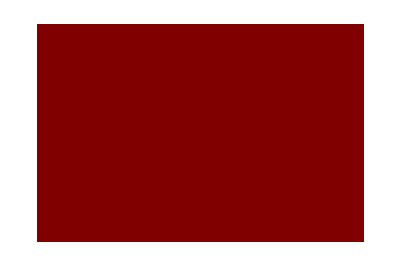

```mathematica
ArrayPlot[{{"R","i","c"},{"h","a","d"}}]
```

```mathematica
Graphics@Raster["R"]
```

```mathematica
board=RandomInteger[10,{3,3}]
```

{{9,7,3},{5,7,8},{5,0,8}}

```mathematica
Dynamic[ClickPane[
Style[
Grid[Table[
Mouseover[
board[[r,c]],
Style[board[[r,c]],FontColor->Orange]
],
{r,1,3},{c,1,3}], Frame->All],
FontSize->30],
(board[[1,1]]=8)&
]
]
```

## Notes

The board is numbers. The player must set all the numbers from start to marker to 8 using only one function. No numbers other than the path can be changed. Helpful suggestions for functions can be given.

The board is a garden and by using certain function you can grow things in your garden.

The player is given the ability to edit the board

```mathematica
Dynamic[ClickPane[
Style[
Grid[Table[
Mouseover[
board[[r,c]],
Style[board[[r,c]],FontColor->Orange]
],
{r,1,3},{c,1,3}], Frame->All],
FontSize->30],
(board[[1,1]]=8)&
]
]
```

```mathematica
board=Array[InputField[7,FieldSize->3]&,{3,3}]
```

{{,,},{,,},{,,}}

```mathematica
Dynamic[Grid[board]]
```

```mathematica
x=InputField["hi"]
```

```mathematica
InputField[Dynamic[x]]
```

```mathematica
board=RandomInteger[9,{15,5}]
```

{{7,7,9,6,1},{7,0,7,6,0},{8,5,2,6,0},{9,5,3,5,4},{5,9,2,4,5},{7,4,3,1,0},{4,8,2,9,9},{9,4,0,4,1},{2,1,2,0,9},{1,5,7,1,6},{0,7,8,9,1},{0,6,3,6,7},{9,0,8,8,7},{3,2,3,7,5},{8,2,3,7,2}}

```mathematica
Dynamic[ArrayPlot[board]]
```

## Notes

The player uses list manipulation functions to dig layers of the matrix you can only edit a highlighted region around your player. Swapping is fine, sometimes you must move to a specific location to get a gem

At first you only have access to Map, but as you collect gems you unlock better tools for digging. The dirt must have some relation to cellular automata.

Use grid and graphics to overlay player in cell

Player always falls down when nothing below their feet. When coding, user must enter modify[rowNumber, pure function] to change arrangement of row

row numbers roll with player. 


Player tries to move right and collect as much gold as possible by entering a set of rules that specify when they should go up, down, or straight. They then press play and their character moves forward following the rules over a random grid. Total score is gold collected at the point when you reach the other side of the board

```mathematica
GridBox[
Array[
Graphics[{Rectangle[]}, Frame->False, ImageSize->10,Frame->All]&,
{4,4}
]
]
```